```mathematica
ClearAll["Global`*"]
```

```mathematica
Ratesfunc[x_] :=(
noise=x[[1]];
ts=x[[2]];
M=x[[3]];
B0=x[[4]];
Bm=x[[5]];
Em=x[[6]];
η=x[[7]];
η2=x[[8]];
λ0=x[[9]];
ef=x[[10]];
γ=x[[11]];
ζ=x[[12]];
f0=x[[13]];
mm0=x[[14]];
growth =N[ts* λ0*M^η2]*(1+RandomReal[{-noise,noise}]) ;
starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])]*(1+RandomReal[{-noise,noise}]);
mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])]*(1+RandomReal[{-noise,noise}]);
recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]*(1+RandomReal[{-noise,noise}]);
maintenance = (ts*ef*B0*M^η)*(1+RandomReal[{-noise,noise}]);
resourcegrowth = ts*0.5*(1+RandomReal[{-noise,noise}]);

{growth,starvation,mortality,recovery,maintenance,resourcegrowth}
)
```

```mathematica
MetapopDyn[α_,λ_,σ_,ρ_,β_,μ_,T_,F0_,H0_,R0_] :=

NDSolve[{
F'[t] ==λ*F[t]-σ*(1-R[t])*F[t] +ρ* R[t] * H[t],
H'[t] ==σ*(1-R[t])*F[t] - ρ* R[t]*H[t] - μ*H[t],
R'[t] ==α*R[t]*(1-R[t]) -(ρ*H[t] + β*F[t])*R[t] ,
F[0]==F0,H[0]==H0,R[0]==R0},{F,H,R},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];
TestThreshold[timeseries_,threshold_]:=If[AnyTrue[timeseries,#<threshold&],1,0];
parameters={
(*noise*)0,
(*ts*)1,
(*M*)Mass =10^2,
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324};
RF =Ratesfunc[parameters];
growth=RF[[1]];
starvation=RF[[2]];
mortality=RF[[3]];
recovery=RF[[4]];
maintenance=RF[[5]];
resourcegrowth=RF[[6]];
(*rhovalues = Table[x,{x,0.2,0.7,0.1}];*)
(*scalevalues = Table[x,{x,6,0.5,-0.6}];*)
sigmavalues =Table[x,{x,starvation/10,starvation/0.4,0.0000005}]
ExtinctionSigma = ParallelTable[
Reps = 2000;
ProportionExtinct=With[{
α=resourcegrowth,λ=growth,σ=sigma,ρ=recovery,β=maintenance,μ=mortality,T=100000000,threshold=15000},
ExtinctionReps = Table[
F0=RandomReal[{1000,30000}];
H0 = RandomReal[{1000,30000}];
R0 = RandomReal[{1000,30000}];
(*Traj=Evaluate[{F[t],H[t],R[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,T,F0,H0,R0] ]*)
Traj=Table[Evaluate[{F[t],H[t],R[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,T,F0,H0,R0]],{t,0,100000000,100000}];
Ftraj = Flatten[Traj,1][[100;;1000,1]];
Htraj = Flatten[Traj,1][[100;;1000,2]];
Rtraj = Flatten[Traj,1][[100;1000,3]];
ConsumerDensity = Htraj + Ftraj;
Extinct=TestThreshold[ConsumerDensity,threshold],
{Reps}];
{sigma/ρ,N[Total[ExtinctionReps]/Reps]}
],
{sigma,sigmavalues}(*,{rho,rhovalues}*)];
```

{4.61204×10^-6,5.11204×10^-6,5.61204×10^-6,6.11204×10^-6,6.61204×10^-6,7.11204×10^-6,7.61204×10^-6,8.11204×10^-6,8.61204×10^-6,9.11204×10^-6,9.61204×10^-6,0.000010112,0.000010612,0.000011112,0.000011612,0.000012112,0.000012612,0.000013112,0.000013612,0.000014112,0.000014612,0.000015112,0.000015612,0.000016112,0.000016612,0.000017112,0.000017612,0.000018112,0.000018612,0.000019112,0.000019612,0.000020112,0.000020612,0.000021112,0.000021612,0.000022112,0.000022612,0.000023112,0.000023612,0.000024112,0.000024612,0.000025112,0.000025612,0.000026112,0.000026612,0.000027112,0.000027612,0.000028112,0.000028612,0.000029112,0.000029612,0.000030112,0.000030612,0.000031112,0.000031612,0.000032112,0.000032612,0.000033112,0.000033612,0.000034112,0.000034612,0.000035112,0.000035612,0.000036112,0.000036612,0.000037112,0.000037612,0.000038112,0.000038612,0.000039112,0.000039612,0.000040112,0.000040612,0.000041112,0.000041612,0.000042112,0.000042612,0.000043112,0.000043612,0.000044112,0.000044612,0.000045112,0.000045612,0.000046112,0.000046612,0.000047112,0.000047612,0.000048112,0.000048612,0.000049112,0.000049612,0.000050112,0.000050612,0.000051112,0.000051612,0.000052112,0.000052612,0.000053112,0.000053612,0.000054112,0.000054612,0.000055112,0.000055612,0.000056112,0.000056612,0.000057112,0.000057612,0.000058112,0.000058612,0.000059112,0.000059612,0.000060112,0.000060612,0.000061112,0.000061612,0.000062112,0.000062612,0.000063112,0.000063612,0.000064112,0.000064612,0.000065112,0.000065612,0.000066112,0.000066612,0.000067112,0.000067612,0.000068112,0.000068612,0.000069112,0.000069612,0.000070112,0.000070612,0.000071112,0.000071612,0.000072112,0.000072612,0.000073112,0.000073612,0.000074112,0.000074612,0.000075112,0.000075612,0.000076112,0.000076612,0.000077112,0.000077612,0.000078112,0.000078612,0.000079112,0.000079612,0.000080112,0.000080612,0.000081112,0.000081612,0.000082112,0.000082612,0.000083112,0.000083612,0.000084112,0.000084612,0.000085112,0.000085612,0.000086112,0.000086612,0.000087112,0.000087612,0.000088112,0.000088612,0.000089112,0.000089612,0.000090112,0.000090612,0.000091112,0.000091612,0.000092112,0.000092612,0.000093112,0.000093612,0.000094112,0.000094612,0.000095112,0.000095612,0.000096112,0.000096612,0.000097112,0.000097612,0.000098112,0.000098612,0.000099112,0.000099612,0.000100112,0.000100612,0.000101112,0.000101612,0.000102112,0.000102612,0.000103112,0.000103612,0.000104112,0.000104612,0.000105112,0.000105612,0.000106112,0.000106612,0.000107112,0.000107612,0.000108112,0.000108612,0.000109112,0.000109612,0.000110112,0.000110612,0.000111112,0.000111612,0.000112112,0.000112612,0.000113112,0.000113612,0.000114112,0.000114612,0.000115112}

NDSolve::ndsz: At t == 790857., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 330465., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 332971., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 256610., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {800000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {400000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {300000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {800000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {400000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {300000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {800000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {400000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {300000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 803371., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 383406., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 133839., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 225760., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 490497., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 368423., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 177659., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 199023., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 284785., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {300000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 356996., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 122518., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 253632., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {300000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 154728., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 197415., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 110896., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {200000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 140648., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 70446., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 20907.7, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 131736., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 273434., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 165362., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {200000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 364395., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 146821., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 25430.4, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 171871., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 52147.3, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 214823., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {300000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 167785., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 211609., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 62099.7, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 228792., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 261905., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 239320., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {300000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 275992., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 64865.5, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 200986., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {300000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 160474., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 53538.2, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 152753., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {200000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 152561., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 174684., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 141925., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {200000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 235186., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 239639., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

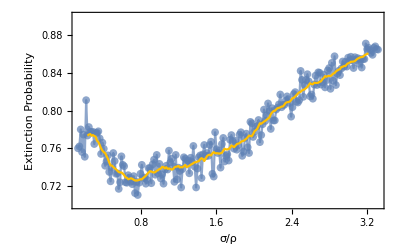

```mathematica
ExtinctionsAllometricPlot=Show[{
ListPlot[ExtinctionSigma,PlotRange->{All,{0.7,0.9}},PlotStyle->Directive[Opacity[0.7]],Frame->True,FrameLabel->{"σ/ρ","Extinction Probability"}],
ListPlot[ExtinctionSigma,PlotRange->{0,1},Joined->True,PlotStyle->Directive[Opacity[0.7]]],
step=15;If[EvenQ[step],step=step+1];
ListPlot[Transpose[{Re[ExtinctionSigma[[1+IntegerPart[N[step/2]];;Length[ExtinctionSigma]-IntegerPart[N[step/2]],1]]],MovingAverage[ExtinctionSigma[[All,2]],step]}],PlotStyle->ColorData[97,8],Joined->True]
}]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_ExtinctionAllometric.pdf",ExtinctionsAllometricPlot,"PDF",ImageResolution->300]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_ExtinctionAllometric.pdf